{‘mode_flip’: False,
 ‘beta_a’: 7.13508841315943,
 ‘alpha_a’: 2.6802985404751,
 ‘gamma_a’: 1.14700754807452,
 ‘phi_a’: 32.0805358660304,
 ‘eta_a’: 6.04437211651708e-06,
 ‘etap_a’: -1.20610240795883e-06,
 ‘beta_b’: 10.1218264042071,
 ‘alpha_b’: -3.56592959662461,
 ‘gamma_b’: 1.35507697330024,
 ‘phi_b’: 30.670911922845,
 ‘eta_b’: -5.1069099780843e-19,
 ‘etap_b’: -2.5011667054117e-19,
 ‘eta_x’: 6.04437211651708e-06,
 ‘etap_x’: -1.20610240795883e-06,
 ‘eta_y’: -5.10705310178987e-19,
 ‘etap_y’: -2.50115336463414e-19}

```mathematica
(*Q14891, Q14901, R11, R12, R33, R34*)
raw = Import["~/data.csv"][[2;;,2;;]];
```

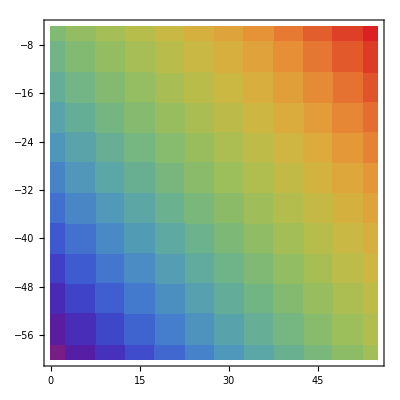

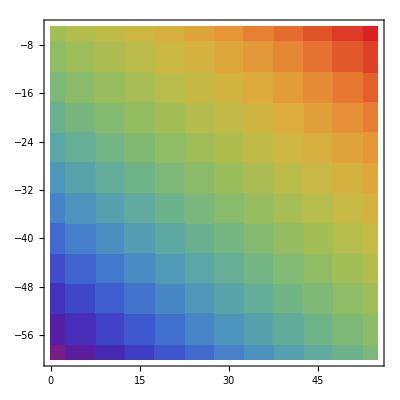

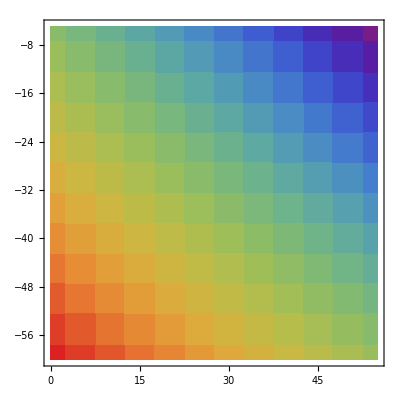

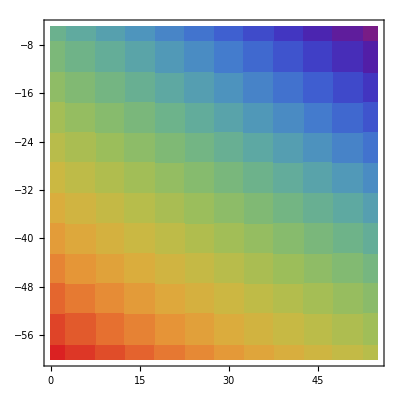

```mathematica
ListDensityPlot[
raw[[All,{1,2,3}]],
ColorFunction->"Rainbow",
InterpolationOrder->0
]
ListDensityPlot[
raw[[All,{1,2,4}]],
ColorFunction->"Rainbow",
InterpolationOrder->0
]
ListDensityPlot[
raw[[All,{1,2,5}]],
ColorFunction->"Rainbow",
InterpolationOrder->0
]
ListDensityPlot[
raw[[All,{1,2,6}]],
ColorFunction->"Rainbow",
InterpolationOrder->0
]
```

twissMatrix[rayMatrix_]:=(
Module[{R11,R12,R21,R22},
{{R11,R12},{R21,R22}}=rayMatrix;

{
{R11^2,-2 R11 R12, R12^2},
{-R11 R21, 1+2 R12 R21, -R12 R22},
{R21^2,-2 R21 R22, R22^2}
}
]
)

 ‘beta_a’: 7.13508841315943,
 ‘alpha_a’: 2.6802985404751,
 ‘gamma_a’: 1.14700754807452,

 ‘beta_b’: 10.1218264042071,
 ‘alpha_b’: -3.56592959662461,
 ‘gamma_b’: 1.35507697330024,

```mathematica
xBetaData = {
#[[1]],
#[[2]],
(#[[3]])^2*7.13-2*#[[3]]*#[[4]]*2.68+(#[[4]])^2*1.147
}&/@raw;
```

```mathematica
yBetaData = {
#[[1]],
#[[2]],
(#[[5]])^2*10.12-2*#[[5]]*#[[6]]*(-3.57)+(#[[6]])^2*1.355
}&/@raw;
```

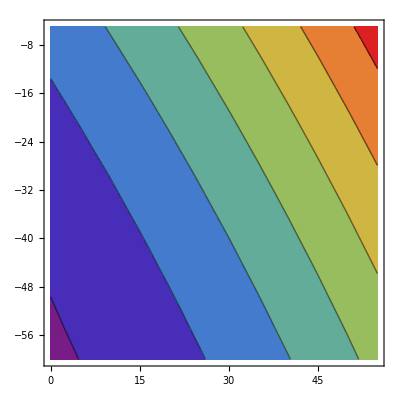

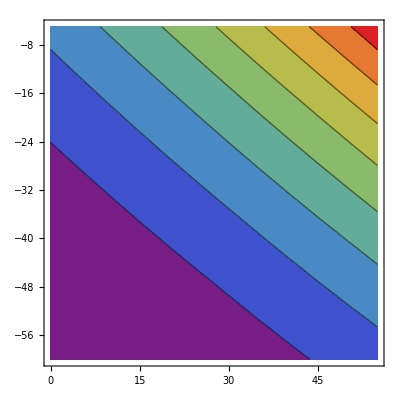

```mathematica
ListContourPlot[
xBetaData,
ColorFunction->"Rainbow",
InterpolationOrder->2
]
ListContourPlot[
yBetaData,
ColorFunction->"Rainbow",
InterpolationOrder->2
]
```